Last modified on: Wednesday, July 11, 2018 at 16:38

Author Info

Hannah Garringer

Kyle Keane, Christopher Wolfram

Wheaton College

Poster Session Content

Textual Analysis of Supreme Court Oral Arguments

This project seeks to determine the correlation between the questions asked by Supreme Court justices during oral argument appeals and justices’ votes to affirm or reverse the decision. Using oral argument transcripts from the past 28 years, this project will primarily utilize Mathematica machine learning to examine these transcripts; attempting to find a mechanism that suggests which way a justice will vote according to the questions asked by said justice in trial. Secondly, this project will examine larger patterns of vote direction in the Supreme Court and suggest further areas of research with this data.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

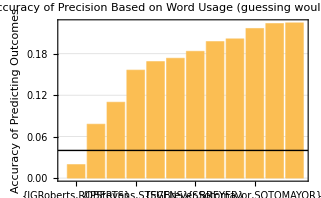

-Word usage is predictive of vote in case
-Characteristic sentiment profile of each justice’s speech

-Further examine the link between emotionally classified language and votes
-Interaction between justices and attorneys

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Sentiment characterization of justices

-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

### Using cached data

#### button

```mathematica
Button[
"Run from here down",
Function[
{cell},
SelectionMove[cell,All,Cell,AutoScroll->False];
FrontEndTokenExecute[EvaluationNotebook[],"EvaluateCells"]
]/@Part[
Cells@EvaluationNotebook[],Position[Cells@EvaluationNotebook[],EvaluationCell[]][[1,1]]+1;;-1
],
Method->"Queued"
]
```

Run from here down

#### Importing local cached data

```mathematica
finalData=Import[FileNameJoin[{NotebookDirectory[],"finalData.wxf"}]];
```

### educational example of looking at a particular justice

#### do it on one to develop code

```mathematica
justice="WHRehnquist";
lastName="REHNQUIST";
```

```mathematica
finalData[[1,"Docket"]];
```

```mathematica
decisions=FirstCase[finalData[[1,"Decisions"]],{justice,theirVote_,fullVote_}:>{theirVote,fullVote}];
```

```mathematica
Cases[finalData[[1,"Conversations"]],{name_/;StringContainsQ[name,lastName],said_}:>said];
```

#### development

```mathematica
getDocket[case_]:=case[["Docket"]]
```

```mathematica
(*this might be Missing[]*)
getDecisions[case_,justice_]:=FirstCase[case[["Decisions"]],{justice,theirVote_,fullVote_}:>{theirVote,fullVote}]
```

```mathematica
getOutcome[case_]:=case[["Decisions",1,3]]
```

```mathematica
getConversations[case_,lastName_]:=Cases[case[["Conversations"]],{name_/;StringContainsQ[name,lastName],said_}:>said]
```

#### eachVote

```mathematica
justiceLastName={{"NMGorsuch","GORSUCH"},{"EKagan","KAGAN"},{"SSotomayor","SOTOMAYOR"},{"SAAlito","ALITO"},{"JGRoberts","ROBERTS"},{"SGBreyer","BREYER"},{"RBGinsburg","GINSBURG"},{"CThomas","THOMAS"},{"DHSouter","SOUTER"},{"AMKennedy","KENNEDY"},{"AScalia","SCALIA"},{"SDOConnor","CONNOR"},{"JPStevens","STEVENS"},{"WHRehnquist","REHNQUIST"},{"LFPowell","POWELL"},{"HABlackmun","BLACKMUN"},{"WEBurger","BURGER"},{"TMarshall","MARSHALL"},{"BRWhite","WHITE"},{"PStewart","STEWART"},{"WJBrennan","BRENNAN"}};
```

```mathematica
finalVote[{justice_,lastName_}]:=Module[
{timelineVote,voteto,associate},
timelineVote={getDecisions[#,justice],getConversations[#,lastName]}&/@finalData;
voteto=DeleteMissing[Union[timelineVote],2]/.{}->{""};
associate=#2->#1&@@@Select[voteto,Length[#]==2&];
associate
]
```

```mathematica
eachvote=AssociationMap[finalVote,justiceLastName];
```

```mathematica
mergedVotes=MapAt[
Replace[
Replace[
#,
{
{1.,n_}:>{1,n},
{2.,n_}:>{2,n},
{3.|4.,n_}:>{3,n},
{5.|6.|7.|"",n_}:>{4,n},
{8.,n_}:>{5,n}
},
{0}
],
{
{n_,2.}:>ToString@{n,2},
{n_,3.}:>ToString@{n,3},
{n_,4.}:>ToString@{n,4},
{n_,5.|6.|7.}:>ToString@{n,5},
{n_,8.|9.|10.}:>ToString@{n,6}
}
]&,
eachvote,
{All,All,2}
];
```

```mathematica
significantConvo=Keys@Select[Map[Length,mergedVotes],#>300&]
```

{{EKagan,KAGAN},{SSotomayor,SOTOMAYOR},{SAAlito,ALITO},{JGRoberts,ROBERTS},{SGBreyer,BREYER},{RBGinsburg,GINSBURG},{DHSouter,SOUTER},{AMKennedy,KENNEDY},{AScalia,SCALIA},{JPStevens,STEVENS},{WHRehnquist,REHNQUIST},{WEBurger,BURGER}}

### bag of words classifier

#### worked example

```mathematica
readyForClassify=MapAt[ToString,MapAt[StringJoin,mergedVotes[{"WHRehnquist","REHNQUIST"}],{All,1}],{All,2}];
```

```mathematica
{trainingData,testingData}=TakeDrop[RandomSample@readyForClassify,IntegerPart[0.8 Length[readyForClassify]]];
```

```mathematica
Length@trainingData
```

1312

```mathematica
fakeJudge=Classify[trainingData]
```

ClassifierFunction[…]

```mathematica
judgeOfFakeJudge=ClassifierMeasurements[fakeJudge,testingData]
```

ClassifierMeasurementsObject[…]

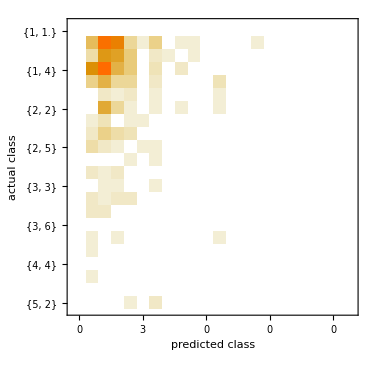

```mathematica
judgeOfFakeJudge["ConfusionMatrixPlot"]
```

### Machine Learning for Each Justice - Pure Text

#### wordBag

```mathematica
wordbag[votes_,{justice_,lastName_}]:=Module[
{readyForClassify,trainingData,testingData,fakeJudge,judgeOfFakeJudge},
readyForClassify=MapAt[ToString,MapAt[StringJoin,votes[{justice,lastName}],{All,1}],{All,2}];
{trainingData,testingData}=TakeDrop[RandomSample@readyForClassify,IntegerPart[0.8 Length[readyForClassify]]];
Length[trainingData];
fakeJudge=Classify[trainingData];
 ClassifierMeasurements[fakeJudge,testingData]
]
```

#### Accuracy of each

```mathematica
classifierMeasurements=AssociationMap[wordbag[mergedVotes,#]&,significantConvo];
```

```mathematica
Counts@RandomChoice[Range@25,1000]/1000//N
```

<|6→0.042,1→0.059,19→0.039,17→0.04,21→0.037,15→0.046,7→0.027,22→0.038,9→0.042,2→0.032,3→0.047,13→0.043,16→0.033,20→0.041,24→0.039,12→0.038,8→0.034,18→0.039,11→0.041,14→0.044,25→0.044,5→0.043,23→0.036,4→0.035,10→0.041|>

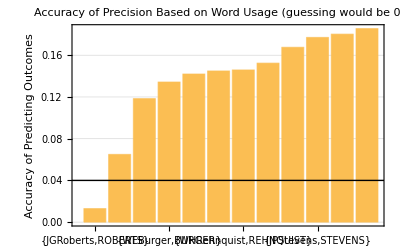

```mathematica
BarChart[Sort@KeyValueMap[Labeled[#2,Rotate[#1,Pi/2]]&,Map[#["Accuracy"]&,classifierMeasurements]],Frame->True,PlotTheme->"Detailed",FrameLabel->"Accuracy of Predicting Outcomes",PlotLabel->"Accuracy of Precision Based on Word Usage\n(guessing would be 0.04)",Epilog->Line[{{0,.04},{10000,.04}}]]
```

### sentiment analysis

#### sentiment

```mathematica
MapAt[Chop@Classify["Sentiment",#,"Probability"->"Negative"]&,mergedVotes[[1]][[2]],{1,All}]
```

{0.201241,1.,0.403824,0.999919,0.201241,0.000247628,0.0991976}→{1, 2}

```mathematica
(*sentiment takes a long time to run*)
sentimentToVote=Map[Function[{vote},MapAt[Chop@Classify["Sentiment",#,"Probability"->"Negative"]&,vote,{1,All}]],KeyTake[mergedVotes,significantConvo],{2}];
```

```mathematica
Length[sentimentToVote]
```

12

```mathematica
Select[sentimentToVote,Length[#]≥300&]//Length
```

12

```mathematica
sentimentToVote[[1]];
```

```mathematica
Rasterize@Dataset[Histogram[Flatten@#[[All,1]],10]&/@sentimentToVote]
```

-Graphics-

```mathematica
Classify["Sentiment",eachvote[[1]][[2]][[1,4]],"Probabilities"]
```

<|Positive→6.32569×10^-15,Neutral→0.000080767,Negative→0.999919|>

```mathematica
eachvote[[1]][[2]][[1,4]]
```

And Coleman sets out the
general rule that ineffective assistance by counsel in
collateral review does not suffice to establish cause
for purposes of Federal habeas. That's the general
rule. And Martinez carves out a small exception for
when there wouldn't be any chance to raise an issue in
State court at all. And that doesn't apply here because
trial court counsel could have raised this issue. We
all admit that.
26
Official - Subject to Final Review
So when we -- when we overrule a precedent,
or part of a precedent, as I think you're effectively
asking us to do with Coleman, we normally don't just ask
about the merits. We also ask about the reliance
interest, the workability, whether the question is
statutory rather than constitutional. And I didn't see
you address any of those factors in your brief. And I'm
wondering what I'm supposed to make of that. Help me
out.

## Rabbit Trails

### Word Frequency

#### Formula

```mathematica
Union[First@StringSplit[#,"-"]&/@sortedFullData[[All,"Docket"]]]
```

Part::pspec1: Part specification Docket is not applicable.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]],-].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[All,-].

Part::pspec1: Part specification Docket is not applicable.

Part::pkspec1: The expression KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[samples,«2»&]]]]&,GroupBy[First[],Symbol[]]] cannot be used as a part specification.

Docket⟦All,KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[samples,Function[{file},StringContainsQ[file,#1]]]]]]&,GroupBy[First[],Symbol[]]]⟧

```mathematica
years=AssociationMap[Interpreter["Date"],If[
StringMatchQ[First@Characters@#,"0"|"1"],
"20"<>#,
"19"<>#
]&/@Union[First@StringSplit[#,"-"]&/@sortedFullData[[All,"Docket"]]]];
```

Part::pspec1: Part specification Docket is not applicable.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]],-].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[All,-].

Part::pspec1: Part specification Docket is not applicable.

Part::pkspec1: The expression KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[samples,«2»&]]]]&,GroupBy[First[],Symbol[]]] cannot be used as a part specification.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[All,0|1].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]],0|1].

Part::pkspec1: The expression If[StringMatchQ[All,0|1],20<>All,19<>All] cannot be used as a part specification.

AssociationMap::invrp: The argument 19Docket⟦If[StringMatchQ[All,0|1],20<>All,19<>All],If[«1»,«1»,19<>KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[«1»]]]&,GroupBy[«1»]]]⟧ is not a valid Association or a list.

```mathematica
docketAndText=sortedFullData[[All,{"Docket","RawText"}]];
```

Part::pspec1: Part specification {Docket,RawText} is not applicable.

```mathematica
wordCounts=Map[
Function[
{entry},
yearAbbreviation=First@StringSplit[entry["Docket"],"-"];
year=If[
StringMatchQ[First@Characters@yearAbbreviation,"0"|"1"],
"20"<>yearAbbreviation,
"19"<>yearAbbreviation
]/.years;
{year,StringCount[entry["RawText"],"technology"]}
],
docketAndText];
```

KeyValueMap::argx: KeyValueMap called with 2 arguments; 1 argument is expected.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]][Docket],-].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]][Docket],0|1].

ReplaceAll::reps: {AssociationMap[Interpreter[Date],19Docket⟦If[StringMatchQ[All,0|1],20<>All,19<>All],If[«1»]⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

KeyValueMap::argx: KeyValueMap called with 2 arguments; 1 argument is expected.

StringCount::strse: String or list of strings expected at position 1 in StringCount[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]][RawText],technology].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[All[Docket],-].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[All[Docket],0|1].

ReplaceAll::reps: {AssociationMap[Interpreter[Date],19Docket⟦If[StringMatchQ[All,0|1],20<>All,19<>All],If[«1»]⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StringCount::strse: String or list of strings expected at position 1 in StringCount[All[RawText],technology].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{Docket,RawText}[Docket],-].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[{Docket,RawText}[Docket],0|1].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

ReplaceAll::reps: {AssociationMap[Interpreter[Date],19Docket⟦If[StringMatchQ[All,0|1],20<>All,19<>All],If[«1»]⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

StringCount::strse: String or list of strings expected at position 1 in StringCount[{Docket,RawText}[RawText],technology].

General::stop: Further output of StringCount::strse will be suppressed during this calculation.

Part::pkspec1: The expression {If[StringMatchQ[All[Docket],0|1],20<>yearAbbreviation,19<>yearAbbreviation]/.AssociationMap[Interpreter[Date],19Docket⟦If[«1»],If[«1»,«1»,19<>«11»[«1»]]⟧],«1»} cannot be used as a part specification.

```mathematica
DateListPlot[Total/@GroupBy[wordCounts,First][[All,All,2]],PlotTheme->"Detailed",PlotLabel->"Occurance of the word \"technology\" in Supreme Court transcripts"]
```

GroupBy::list1: The argument «1» is not a valid list of Associations or rules or lists of rules.

Part::pkspec1: The expression StringCount[All[RawText],technology] cannot be used as a part specification.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

GroupBy::list1: The argument StringCount[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[«1»]]]&,GroupBy[First[],Symbol[]]][RawText],technology]⟦StringCount[«1»],«1»⟧ is not a valid list of Associations or rules or lists of rules.

GroupBy::list1: The argument StringCount[All[RawText],technology]+StringCount[KeyValueMap[Association[Docket→#1,«1»,RawText→«1»]&,«1»][…],«12»]+StringCount[{Docket,RawText}[RawText],technology] is not a valid list of Associations or rules or lists of rules.

General::stop: Further output of GroupBy::list1 will be suppressed during this calculation.

DateListPlot::ldata: GroupBy[StringCount[All[RawText],technology]+StringCount[KeyValueMap[«1»&,GroupBy[First[],Symbol[]]][RawText],…y]+StringCount[{Docket,RawText}[RawText],technology],0] is not a valid dataset or list of datasets.

DateListPlot[GroupBy[StringCount[All[RawText],technology]+StringCount[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[samples,Function[{file},StringContainsQ[file,#1]]]]]]&,GroupBy[First[],Symbol[]]][RawText],technology]+StringCount[{Docket,RawText}[RawText],technology],0],PlotTheme→Detailed,PlotLabel→Occurance of the word "technology" in Supreme Court transcripts]

#### Function

```mathematica
wordFrequency[docketAndText_,yearDict_,searchWordList_]:=Module[
{wordCounts,yearAbbreviation,year},
wordCounts=Map[
Function[
{entry},
yearAbbreviation=First@StringSplit[entry["Docket"],"-"];
year=If[
StringMatchQ[First@Characters@yearAbbreviation,"0"|"1"],
"20"<>yearAbbreviation,
"19"<>yearAbbreviation
]/.years;
{year,StringCount[entry["RawText"],searchWordList]}
],
docketAndText];

DateListPlot[Total/@GroupBy[wordCounts,First][[All,All,2]],PlotTheme->"Monochrome",PlotLabel->"Occurances of "<>ToString@searchWordList<>" in Supreme Court transcripts"]
]
```

```mathematica
years=AssociationMap[Interpreter["Date"],If[
StringMatchQ[First@Characters@#,"0"|"1"],
"20"<>#,
"19"<>#
]&/@Union[First@StringSplit[#,"-"]&/@sortedFullData[[All,"Docket"]]]];
```

Part::pspec1: Part specification Docket is not applicable.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]],-].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[All,-].

Part::pspec1: Part specification Docket is not applicable.

Part::pkspec1: The expression KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[samples,«2»&]]]]&,GroupBy[First[],Symbol[]]] cannot be used as a part specification.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[All,0|1].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]],0|1].

Part::pkspec1: The expression If[StringMatchQ[All,0|1],20<>All,19<>All] cannot be used as a part specification.

AssociationMap::invrp: The argument 19Docket⟦If[StringMatchQ[All,0|1],20<>All,19<>All],If[«1»,«1»,19<>KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[«1»]]]&,GroupBy[«1»]]]⟧ is not a valid Association or a list.

```mathematica
docketAndText=sortedFullData[[All,{"Docket","RawText"}]];
```

Part::pspec1: Part specification {Docket,RawText} is not applicable.

```mathematica
wordFrequency[docketAndText,years,"religious"]
```

KeyValueMap::argx: KeyValueMap called with 2 arguments; 1 argument is expected.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]][Docket],-].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]][Docket],0|1].

ReplaceAll::reps: {AssociationMap[Interpreter[Date],19Docket⟦If[StringMatchQ[All,0|1],20<>All,19<>All],If[«1»]⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

KeyValueMap::argx: KeyValueMap called with 2 arguments; 1 argument is expected.

StringCount::strse: String or list of strings expected at position 1 in StringCount[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]][RawText],religious].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[All[Docket],-].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[All[Docket],0|1].

ReplaceAll::reps: {AssociationMap[Interpreter[Date],19Docket⟦If[StringMatchQ[All,0|1],20<>All,19<>All],If[«1»]⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

StringCount::strse: String or list of strings expected at position 1 in StringCount[All[RawText],religious].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{Docket,RawText}[Docket],-].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[{Docket,RawText}[Docket],0|1].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

ReplaceAll::reps: {AssociationMap[Interpreter[Date],19Docket⟦If[StringMatchQ[All,0|1],20<>All,19<>All],If[«1»]⟧]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

StringCount::strse: String or list of strings expected at position 1 in StringCount[{Docket,RawText}[RawText],religious].

General::stop: Further output of StringCount::strse will be suppressed during this calculation.

Part::pkspec1: The expression {If[StringMatchQ[All[Docket],0|1],20<>yearAbbreviation$1977771,19<>yearAbbreviation$1977771]/.AssociationMap[Interpreter[Date],19Docket⟦If[«1»],If[«1»]⟧],«1»} cannot be used as a part specification.

GroupBy::list1: The argument «1» is not a valid list of Associations or rules or lists of rules.

Part::pkspec1: The expression StringCount[All[RawText],religious] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

GroupBy::list1: The argument StringCount[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[«1»]]]&,GroupBy[First[],Symbol[]]][RawText],religious]⟦«1»,StringCount[{…t,…}[…t],«11»]⟧ is not a valid list of Associations or rules or lists of rules.

GroupBy::list1: The argument StringCount[All[RawText],religious]+StringCount[KeyValueMap[Association[Docket→#1,…→#2,RawText→«1»]&,«1»][…t],«11»]+StringCount[{Docket,RawText}[RawText],religious] is not a valid list of Associations or rules or lists of rules.

General::stop: Further output of GroupBy::list1 will be suppressed during this calculation.

DateListPlot::ldata: GroupBy[StringCount[All[RawText],religious]+«1»+StringCount[{Docket,RawText}[RawText],religious],0] is not a valid dataset or list of datasets.

DateListPlot[GroupBy[StringCount[All[RawText],religious]+StringCount[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[samples,Function[{file},StringContainsQ[file,#1]]]]]]&,GroupBy[First[],Symbol[]]][RawText],religious]+StringCount[{Docket,RawText}[RawText],religious],0],PlotTheme→Monochrome,PlotLabel→Occurances of religious in Supreme Court transcripts]

#### Microsite

```mathematica
CloudPut[docketAndText,"junk/data"];
```

```mathematica
CloudGet["junk/data"];
```

First::argt: First called with 0 arguments; 1 or 2 arguments are expected.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

GroupBy::list1: The argument First[] is not a valid list of Associations or rules or lists of rules.

KeyValueMap::invak: The argument GroupBy[First[],Symbol[]] is not a valid Association.

Part::pspec1: Part specification {Docket,RawText} is not applicable.

```mathematica
With[
{yearDict=years},
CloudDeploy[
FormPage[
{"Terms"->"String"},
Function[
{formValues},
passThis=CloudGet["junk/data"];
terms=StringSplit[formValues["Terms"],","];
wordFrequency[passThis,yearDict,terms]
]],
"junk/test",
Permissions->"Public"
]
]
```

CloudObject[https://www.wolframcloud.com/objects/hannah.r.garringer/junk/test]

#### Word count

```mathematica
theySaidWhat=Rule@@@Cases[grouped,{_,_}];
```

```mathematica
sentimentMap=MapAt[Length@TextCases[#,"Word"]&,theySaidWhat,{All,2}];
```

```mathematica
ListPlot@Part[sentimentMap,All,2]
```

Part::partw: Part 2 of Length[TextCases[#1,Word]]& does not exist.

ListPlot::lpn: MapAt[Length[TextCases[#1,Word]]&,{},{All,2.}]⟦All,2⟧ is not a list of numbers or pairs of numbers.

ListPlot[MapAt[Length[TextCases[#1,Word]]&,{},{All,2}]⟦All,2⟧]

```mathematica
q=Flatten[Normal[sortedFullData]];
```

```mathematica
Take[ReverseSort[Counts[Tally[q]]],200]
```

Tally::list: List expected at position 1 in Tally[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]]].

Counts::invl: The argument Tally[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]]] is not a list.

Take::take: Cannot take positions 1 through 200 in Counts[Tally[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[«1»]]]&,GroupBy[First[],Symbol[]]]]].

Take[Counts[Tally[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[samples,Function[{file},StringContainsQ[file,#1]]]]]]&,GroupBy[First[],Symbol[]]]]],200]

### Machine Learning Word

#### Word Frequency Prediction

```mathematica
features=Function[
{text},
{StringCount[text,"liberal"],StringCount[text,"constitution"]}
]/@sortedFullData[[All,"RawText"]];
```

Part::pspec1: Part specification RawText is not applicable.

StringCount::strse: String or list of strings expected at position 1 in StringCount[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]],liberal].

StringCount::strse: String or list of strings expected at position 1 in StringCount[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[«2»]]]]&,GroupBy[First[],Symbol[]]],constitution].

StringCount::strse: String or list of strings expected at position 1 in StringCount[All,liberal].

General::stop: Further output of StringCount::strse will be suppressed during this calculation.

Part::pkspec1: The expression {StringCount[All,liberal],StringCount[All,constitution]} cannot be used as a part specification.

```mathematica
outcomes=First/@sortedFullData[[All,"Decisions",All,3]];
```

Part::pspec1: Part specification Decisions is not applicable.

First::normal: Nonatomic expression expected at position 1 in First[All].

First::normal: Nonatomic expression expected at position 1 in First[Decisions].

First::normal: Nonatomic expression expected at position 1 in First[All].

General::stop: Further output of First::normal will be suppressed during this calculation.

Part::pkspec1: The expression First[All] cannot be used as a part specification.

```mathematica
fakeJudge=Classify[features->outcomes]
```

Classify::mlbddata: The data is not formatted correctly.

Classify[{StringCount[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[samples,Function[{file},StringContainsQ[file,#1]]]]]]&,GroupBy[First[],Symbol[]]],liberal],StringCount[KeyValueMap[Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[samples,Function[{file},StringContainsQ[file,#1]]]]]]&,GroupBy[First[],Symbol[]]],constitution]}⟦{StringCount[All,liberal],StringCount[All,constitution]},{0,0}⟧→(Association[Docket→#1,Decisions→#2,RawText→Import[First[Select[samples,Function[{file},StringContainsQ[file,#1]]]]]]&)⟦First[All],First[Decisions],First[All],First[3]⟧]

```mathematica
ListLinePlot[Table[fakeJudge[{0,x},"Probability"->2.],{x,0,100}],PlotRange->{0,1}]
```

-Graphics-

```mathematica
ListLinePlot@Table[fakeJudge[{x,0}],{x,0,100}]
```

-Graphics-

```mathematica
(*TRY: Malign, Inaccurate, Basic rights, Alien*)
```

### Text Associations

#### Names to text

```mathematica
data=Association@Map[FileBaseName[#]->Import[#]&,samples];
```

Import::infer: Cannot infer format of file .DS_Store.

```mathematica
exampleText=data[[1]];
```

```mathematica
StringSplit[exampleText,letter:Repeated[CharacterRange["A","Z"]]~~":":>letter<>":"];
```

```mathematica
splitAtProceedings=StringSplit[exampleText,"P R O C E E D I N G S"];
```

```mathematica
hasProceedings=Length@splitAtProceedings===2
```

False

```mathematica
transcripts=splitAtProceedings[[2]];
```

```mathematica
chars=Join[CharacterRange["A","Z"],{Whitespace,"."}]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,Whitespace,.}

```mathematica
names=StringTrim@StringCases[transcripts,name:Repeated[chars]~~":":>name];
ReverseSort@Counts@names;
```

StringTrim::strse: String or list of strings expected at position 1 in StringTrim[{{}}].

Counts::invl: The argument StringTrim[{{}}] is not a list.

#### Individual statements

```mathematica
transc=StringReplace[transcripts,".\n"->" "];
```

```mathematica
grouped=StringTrim/@Split[StringSplit[transc,name:Repeated[chars]~~":":>name],StringMatchQ[#,Repeated[chars]]&];
justwords=Delete[grouped,1];
```

StringTrim::strse: String or list of strings expected at position 1 in StringTrim[{{35_Orig_12-12-1985.txt}}].

```mathematica
groupedstat=GatherBy[justwords,First];
```

```mathematica
petitioner=StringDelete[DigitCharacter][Flatten@groupedstat[[2]]];
```

Part::partw: Part 2 of {} does not exist.

StringDelete::strse: String or list of strings expected at position 1 in StringDelete[DigitCharacter][{}⟦2⟧].

```mathematica
nonumbers1=StringDelete[DigitCharacter][Flatten@grouped];
```

StringDelete::strse: String or list of strings expected at position 1 in StringDelete[DigitCharacter][{StringTrim[{{35_Orig_12-12-1985.txt}}]}].

#### Emotion measures

```mathematica
ListLinePlot[{MeanFilter[ReplaceAll[Classify["Sentiment",nonumbers1],{"Positive"->1,"Negative"->-1,Indeterminate->0,"Neutral"->0}],10]},PlotRange->All,Joined->True]
```

ClassifierFunction::mlincfttp: Incompatible variable type (Text) and variable value (StringDelete[DigitCharacter][{StringTrim[{{35_Orig_12-12-1985.txt}}]}]).

MeanFilter::arg1: The first argument … is neither a rectangular array nor an image.

SeedRandom::seed: Argument 1234. in SeedRandom[1234.] should be an integer or a string.

ClassifierFunction::mlincfttp: Incompatible variable type (Text) and variable value (StringDelete[DigitCharacter][{StringTrim[{{35_Orig_12-12-1985.txt}}]}]).

General::stop: Further output of ClassifierFunction::mlincfttp will be suppressed during this calculation.

MeanFilter::arg1: The first argument … is neither a rectangular array nor an image.

SeedRandom::seed: Argument 1234. in SeedRandom[1234.] should be an integer or a string.

MeanFilter::arg1: The first argument … is neither a rectangular array nor an image.

General::stop: Further output of MeanFilter::arg1 will be suppressed during this calculation.

SeedRandom::seed: Argument 1234. in SeedRandom[1234.] should be an integer or a string.

General::stop: Further output of SeedRandom::seed will be suppressed during this calculation.

-Graphics-

```mathematica
Mean@ReplaceAll[Classify["Sentiment",nonumbers1],{"Positive"->1,"Negative"->-1,Indeterminate->0,"Neutral"->0}]//N
```

ClassifierFunction::mlincfttp: Incompatible variable type (Text) and variable value (StringDelete[DigitCharacter][{StringTrim[{{35_Orig_12-12-1985.txt}}]}]).

SeedRandom::seed: Argument 1234. in SeedRandom[1234.] should be an integer or a string.

ClassifierFunction::mlincfttp: Incompatible variable type (Text) and variable value (StringDelete[DigitCharacter][{StringTrim[{{35_Orig_12-12-1985.txt}}]}]).

General::stop: Further output of ClassifierFunction::mlincfttp will be suppressed during this calculation.

Mean[ClassifierFunction[…][StringDelete[DigitCharacter][{StringTrim[{{35_Orig_12-12-1985.txt}}]}],BatchProcessing→Automatic,TieBreakerFunction→RandomChoice,ClassPriors→Automatic,IndeterminateThreshold→Automatic,PerformanceGoal→Automatic,RandomSeeding→1234.,TargetDevice→CPU,UtilityFunction→Automatic]]

```mathematica
plotemotion[emotion_String]:=ListLinePlot[{MeanFilter[ReplaceAll[Classify["Sentiment",emotion],{"Positive"->1,"Negative"->-1,Indeterminate->0,"Neutral"->0}],10]},PlotRange->All,Joined->True]
plotemotionmean[mean_String]:=Mean@ReplaceAll[Classify["Sentiment",mean]]
```

### Data Visualization

#### Liberal/Conservative

```mathematica
libcon=Position[decisionData[[1]],"docket"|"dateArgument"|"decisionDirection",{1}]
```

Part::partd: Part specification decisionData⟦1⟧ is longer than depth of object.

{}

```mathematica
goodexcel2=Part[decisionData,All,libcon]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

```mathematica
matchedcases2=Select[goodexcel2,MemberQ[caseNumbersFromTranscripts,#[[1]]]&];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
singlematchedcases2=Union@matchedcases2;
```

```mathematica
datedecision2=Transpose@Delete[Transpose@singlematchedcases2,List/@{1}];
```

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
findatedecision2=Drop[Sort[datedecision2],1;;16];
```

Drop::drop: Cannot drop positions 1 through 16 in Transpose[Transpose[]].

```mathematica
dataplot2=SplitBy[SortBy[findatedecision2,Last],Last];
```

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[1;;16,Transpose[Transpose[]]].

```mathematica
liberal=;
con=;
```

Delete::partw: Part {2} of Transpose[1;;16] does not exist.

DateValue::arg: Argument Transpose[Delete[Transpose[1;;16],{{2}}]] cannot be interpreted as a date or time input

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[1;;16],{{2}}]]]].

Delete::partw: Part {2} of Transpose[Transpose[Transpose[]]] does not exist.

DateValue::arg: Argument Transpose[Delete[Transpose[Transpose[Transpose[]]],{{2}}]] cannot be interpreted as a date or time input

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[Transpose[Transpose[]]],{{2}}]]]].

```mathematica
DateListPlot[{liberal,con},PlotTheme->"Detailed",FrameTicks->{DateRange[DateObject[{1980},"Year","Gregorian",-4.],DateObject[{2016},"Year","Gregorian",-4.],Quantity[5,"Years"]],Automatic},PlotLegends->{"liberal","con"}]
```

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {Tally[DateValue[{Year},Transpose[Delete[Transpose[1;;16],{{2}}]]]],Tally[DateValue[{Year},Transpose[Delete[Transpose[Transpose[Transpose[]]],{{2}}]]]]} is not a valid dataset or list of datasets.

DateListPlot[{Tally[DateValue[{Year},Transpose[Delete[Transpose[1;;16],{{2}}]]]],Tally[DateValue[{Year},Transpose[Delete[Transpose[Transpose[Transpose[]]],{{2}}]]]]},PlotTheme→Detailed,FrameTicks→{{Year: 1980,Year: 1985,Year: 1990,Year: 1995,Year: 2000,Year: 2005,Year: 2010,Year: 2015},Automatic},PlotLegends→{liberal,con}]

#### Total vote direction

```mathematica
excelheaders=Flatten@Position[numericData[[1]],"docket"|"dateArgument"|"caseDisposition",{1}];
```

```mathematica
goodexcel=Part[numericData,All,excelheaders];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

First::nofirst: Symbol[] has zero length and no first element.

```mathematica
matchedcases=Select[goodexcel,MemberQ[caseNumbersFromTranscripts,#[[1]]]&];
```

Part::partw: Part 1 of Symbol[] does not exist.

First::argt: First called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
singlematchedcases=Union@matchedcases;
```

```mathematica
datedecision=Transpose@Delete[Transpose@singlematchedcases,List/@{1}];
```

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

```mathematica
findatedecision=Drop[Sort[datedecision],1;;16];
```

Drop::drop: Cannot drop positions 1 through 16 in Transpose[Transpose[]].

```mathematica
assoc=#1->#2&@@@findatedecision;
```

Function::slotn: Slot number 2 in #1→#2& cannot be filled from (#1→#2&)[Transpose[]].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[Transpose[]→#2,1→16].

```mathematica
finaldatedecision=SplitBy[SortBy[assoc,Last],Last];
```

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[1→16,Transpose[]→#2].

```mathematica
two=Extract[finaldatedecision,1];
three=Extract[finaldatedecision,2];
four=Extract[finaldatedecision,3];
five=Extract[finaldatedecision,4];
six=Extract[finaldatedecision,5];
seven=Extract[finaldatedecision,6];
eight=Extract[finaldatedecision,7];
nine=Extract[finaldatedecision,8];
ten=Extract[finaldatedecision,9];
```

Extract::partw: Part 3 of Drop[1→16,Transpose[]→#2] does not exist.

Extract::partw: Part 4 of Drop[1→16,Transpose[]→#2] does not exist.

Extract::partw: Part 5 of Drop[1→16,Transpose[]→#2] does not exist.

Extract::partw: Part 6 of Drop[1→16,Transpose[]→#2] does not exist.

Extract::partw: Part 7 of Drop[1→16,Transpose[]→#2] does not exist.

Extract::partw: Part 8 of Drop[1→16,Transpose[]→#2] does not exist.

Extract::partw: Part 9 of Drop[1→16,Transpose[]→#2] does not exist.

Function::slotn: Slot number 2 in #1& cannot be filled from (#1&)[Missing[NotAvailable]].

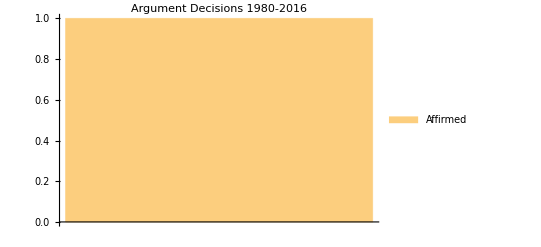

```mathematica
DateHistogram[{two,three,four,five,six,seven,eight,nine,ten},"Year",DateTicksFormat->{"","","Year"},ChartLegends->{"Affirmed","Reversed","Reversed & Remanded","Vacated & Remanded","Affirmed & Reversed in Part","Affirmed & Reversed in Part & Remanded","Vacated","Petition Denied","Certification to/from Lower Court"},Ticks->{DateRange[DateObject[{1980},"Year","Gregorian",-4.],DateObject[{2016},"Year","Gregorian",-4.],Quantity[5,"Years"]],Automatic},ChartLabels->Placed[{"Argument Decisions 1980-2016"},Above]]
```

```mathematica
dataplot=SplitBy[SortBy[findatedecision,Last],Last];
```

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[1;;16,Transpose[Transpose[]]].

```mathematica
twoP=;
threeP=;
fourP=;
fiveP=;
sixP=;
sevenP=;
eightP=;
nineP=;
tenP=;
```

Delete::partw: Part {2} of Transpose[1;;16] does not exist.

DateValue::arg: Argument Transpose[Delete[Transpose[1;;16],{{2}}]] cannot be interpreted as a date or time input

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[1;;16],{{2}}]]]].

Delete::partw: Part {2} of Transpose[Transpose[Transpose[]]] does not exist.

DateValue::arg: Argument Transpose[Delete[Transpose[Transpose[Transpose[]]],{{2}}]] cannot be interpreted as a date or time input

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[Transpose[Transpose[]]],{{2}}]]]].

Extract::partw: Part 3 of Drop[1;;16,Transpose[Transpose[]]] does not exist.

Delete::partw: Part {2} of Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],3]] does not exist.

DateValue::arg: Argument Transpose[Delete[Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],3]],{{2}}]] cannot be interpreted as a date or time input

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[Extract[Drop[Span[«2»],Transpose[«1»]],3]],{{2}}]]]].

Extract::partw: Part 4 of Drop[1;;16,Transpose[Transpose[]]] does not exist.

Delete::partw: Part {2} of Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],4]] does not exist.

DateValue::arg: Argument Transpose[Delete[Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],4]],{{2}}]] cannot be interpreted as a date or time input

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[Extract[Drop[Span[«2»],Transpose[«1»]],4]],{{2}}]]]].

Extract::partw: Part 5 of Drop[1;;16,Transpose[Transpose[]]] does not exist.

Delete::partw: Part {2} of Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],5]] does not exist.

DateValue::arg: Argument Transpose[Delete[Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],5]],{{2}}]] cannot be interpreted as a date or time input

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[Extract[Drop[Span[«2»],Transpose[«1»]],5]],{{2}}]]]].

Extract::partw: Part 6 of Drop[1;;16,Transpose[Transpose[]]] does not exist.

Delete::partw: Part {2} of Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],6]] does not exist.

DateValue::arg: Argument Transpose[Delete[Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],6]],{{2}}]] cannot be interpreted as a date or time input

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[Extract[Drop[Span[«2»],Transpose[«1»]],6]],{{2}}]]]].

Extract::partw: Part 7 of Drop[1;;16,Transpose[Transpose[]]] does not exist.

Delete::partw: Part {2} of Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],7]] does not exist.

DateValue::arg: Argument Transpose[Delete[Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],7]],{{2}}]] cannot be interpreted as a date or time input

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[Extract[Drop[Span[«2»],Transpose[«1»]],7]],{{2}}]]]].

Extract::partw: Part 8 of Drop[1;;16,Transpose[Transpose[]]] does not exist.

Delete::partw: Part {2} of Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],8]] does not exist.

DateValue::arg: Argument Transpose[Delete[Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],8]],{{2}}]] cannot be interpreted as a date or time input

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[Extract[Drop[Span[«2»],Transpose[«1»]],8]],{{2}}]]]].

Extract::partw: Part 9 of Drop[1;;16,Transpose[Transpose[]]] does not exist.

Delete::partw: Part {2} of Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],9]] does not exist.

DateValue::arg: Argument Transpose[Delete[Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],9]],{{2}}]] cannot be interpreted as a date or time input

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[Extract[Drop[Span[«2»],Transpose[«1»]],9]],{{2}}]]]].

```mathematica
tenP//Normal
```

Tally[DateValue[{Year},Transpose[Delete[Transpose[Extract[Drop[1;;16,Transpose[Transpose[]]],9]],{{2}}]]]]

```mathematica
DateRange[DateObject[{1980},"Year","Gregorian",-4.],DateObject[{2016},"Year","Gregorian",-4.],Quantity[5,"Years"]]
```

{Year: 1980,Year: 1985,Year: 1990,Year: 1995,Year: 2000,Year: 2005,Year: 2010,Year: 2015}

```mathematica
DateListPlot[{twoP,threeP,fourP,fiveP,sixP,sevenP,eightP,nineP,tenP},"Year",DateTicksFormat->{" ", " ", "Year"},PlotLegends->{"Affirmed","Reversed","Reversed & Remanded","Vacated & Remanded","Affirmed & Reversed in Part","Affirmed & Reversed in Part & Remanded","Vacated","Petition Denied","Certification to/from Lower Court"},FrameLabel->"Argument Decisions 1980-2016",FrameTicks->{DateRange[DateObject[{1980},"Year","Gregorian",-4.],DateObject[{2016},"Year","Gregorian",-4.],Quantity[5,"Years"]],Automatic}]
```

Delete::psl: Position specification 2. in Transpose[1.;;16.] is not a machine-sized integer or a list of machine-sized integers.

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[1.;;16.],{{2.}}]]]].

Delete::psl: Position specification 2. in Transpose[Transpose[Transpose[]]] is not a machine-sized integer or a list of machine-sized integers.

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[Transpose[Transpose[]]],{{2.}}]]]].

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[1.;;16.,Transpose[Transpose[]]].

Extract::partw: Part 3 of Drop[1.;;16.,Transpose[Transpose[]]] does not exist.

Delete::psl: Position specification 2. in Transpose[Extract[Drop[1.;;16.,Transpose[Transpose[]]],3]] is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

DateValue::arg: Argument {Year} cannot be interpreted as a date or time input

General::stop: Further output of DateValue::arg will be suppressed during this calculation.

Tally::list: List expected at position 1 in Tally[DateValue[{Year},Transpose[Delete[Transpose[Extract[Drop[Span[«2»],Transpose[«1»]],3]],{{2.}}]]]].

General::stop: Further output of Tally::list will be suppressed during this calculation.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[1.;;16.,Transpose[Transpose[]]].

Extract::partw: Part 4 of Drop[1.;;16.,Transpose[Transpose[]]] does not exist.

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[1.;;16.,Transpose[Transpose[]]].

General::stop: Further output of Drop::seqs will be suppressed during this calculation.

Extract::partw: Part 5 of Drop[1.;;16.,Transpose[Transpose[]]] does not exist.

General::stop: Further output of Extract::partw will be suppressed during this calculation.

-Graphics-

```mathematica
finaldecision=Flatten@findatedecision[[All,2]];
```

Part::partw: Part 2 of Transpose[Transpose[]] does not exist.

```mathematica
Plot[PDF[SmoothKernelDistribution[finaldecision],x],{x,1,10},FrameTicks->{Range@10,Automatic},Filling->Axis,FrameLabel->"Distribution of Votes 1980-2016",PlotTheme->"Detailed",PlotLegends->None]
```

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[Drop[Transpose[Transpose[]],1;;16]⟦All,2⟧] should be a vector or a matrix of real numbers or a valid TemporalData object.

-Graphics-